# Trapped-Ions Oxford/Hub virtual device

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz

```mathematica
Options[TrappedIonOxford]={
(*the nodes name together with the total qubits on each node*)
Nodes-><|"Alice"->4,"Bob"->4|>,
T1-><|"Alice"->100, "Bob"->110 |>,
T2-><|"Alice"->40, "Bob"->45|>,
(* duration for moving operations: Split,Combine, and physical swap*)
DurMove-><|"Alice"->4, "Bob"->5|>,

(*fidelity of preparation/initialisation*)
FidInit-><|"Alice"->0.99, "Bob"->0.98|>,
(*fraction of depolarising:dephasing in the initialisation *)
EFInit-><|"Alice"->{1,0}, "Bob"->{1,0}|>,
DurInit-><|"Alice"->2,"Bob"->5|>,

(* Readout: fidelity. It has bitflip error 
Scattering error affecting the neighborhood qubits, e.g., collaps the superposition into 0
*)
FidRead-><|"Alice"->0.98, "Bob"->0.99|>,
DurRead-><|"Alice"->20, "Bob"->20|>,

(*Fidelity of single x- and y- rotations; z-rotation is instaneous (noiseless, virtual)
future:Set manually the error coefficient instead of setting the fidelity at the first place.
Future: off-resonant oscillation in the same zone
 *)
FidSingleXY-><|"Alice"->0.9999, "Bob"->0.99999|>,
(*fraction of depolarising:dephasing noise of the x- and y- rotations *)
EFSingleXY-><|"Alice"->{1,0},"Bob"->{0.9,0.1}|>,

(* rabi frequency on single rotations in MHz *)
RabiFreq-><|"Alice"->5, "Bob"->5 |>,

(* frequency of CZ operation*)
FreqCZ-><|"Alice"->5*10^3,"Bob"->3.3*10^3|>,
(*Fidelity of controlled-Z operation *)
FidCZ-><|"Alice"->0.97, "Bob"->0.96|>,
EFCZ-><|"Alice"->{1,0},"Bob"->{0,1}|>,
(* frequency of remote entanglement *)
FreqEnt->6*10^3,
(* fidelity of remote entanglement *)
FidEnt->0.8,
EFEnt->{1,0}
};
```

Commonly defined standard gates that can be easily composed to the native Trapped ion gates

```mathematica
StdGates::usage="Replacements for standard gates that are straightforwardly composable to the native trapped ions gates";
StdGates={Subscript[H, q_][n_]:>Sequence@@{Subscript[Rx, q][n,π],Subscript[Ry, q][n,-π/2]}};
```

[Native Gates]
 Init_q[node], Read_q[node], Rx_q[node,θ], Ry_q[node,θ], CZ_(q1,q2)[node], Ent[node1, node2], SWAPLoc_(q1,q2)[node], Splz_(q1,q2)[node,zone_destination], Comb_(q1,q2)[node], Comb_(q1,q2)[node,zone_destination]

[Zone and operations]
Zone 1 : prepare, store?, detect
Zone 2 : prepare, store?, detect, logic
Zone 3 : prepare, store?, detect, logic
Zone 4 : remote entangle

The device initialised with a connected ions in the zone 1.

```mathematica
dev=TrappedIonOxford[];
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

The total circuit and moves until page 38. The expected result is qubit 4 at zone 2 is highly entangled after 3 distillations .

```mathematica
circ={Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3],Subscript[Init, 3]["Alice"],Subscript[Init, 4]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Init, 4]["Bob"],Subscript[Splz, 3,4]["Alice",4],Subscript[Splz, 3,4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"],Subscript[Comb, 3,4]["Alice",3],Subscript[Comb, 3,4]["Bob",3],Subscript[SWAPLoc, 3,4]["Alice"],Subscript[SWAPLoc, 3,4]["Bob"],Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[Comb, 4,3]["Alice",3],Subscript[Comb, 4,3]["Bob",3],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Splz, 4,3]["Alice",2],Subscript[Splz, 4,3]["Bob",2],Subscript[Init, 1]["Alice"],Subscript[Init, 1]["Bob"],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],Subscript[Splz, 1,2]["Alice",2],Subscript[Splz, 1,2]["Bob",2],Subscript[Init, 3]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Comb, 2,4]["Alice"],Subscript[Comb, 2,4]["Bob"],Subscript[Shutl, 3]["Alice",4],Subscript[Shutl, 3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[SWAPLoc, 2,4]["Alice"],Subscript[SWAPLoc, 2,4]["Bob"],Subscript[Splz, 4,2]["Alice",3],Subscript[Splz, 4,2]["Bob",3],Subscript[Comb, 2,3]["Alice",3],Subscript[Comb, 2,3]["Bob",3],Subscript[SWAPLoc, 2,3]["Alice"],Subscript[SWAPLoc, 2,3]["Bob"],Subscript[Splz, 3,2]["Alice",4],Subscript[Splz, 3,2]["Bob",4],
Subscript[Ent, 2,2]["Alice","Bob"],Subscript[Comb, 3,2]["Alice",3],Subscript[Comb, 3,2]["Bob",3],Subscript[CZ, 3,2]["Alice"],Subscript[CZ, 3,2]["Bob"],Subscript[Splz, 3,2]["Alice",2],Subscript[Splz, 3,2]["Bob",2],Subscript[Comb, 4,3]["Alice"],Subscript[CZ, 4,3]["Alice"],Subscript[Comb, 4,3]["Bob"],Subscript[CZ, 4,3]["Bob"],Subscript[Read, 2]["Alice"],Subscript[Read, 2]["Bob"],Subscript[H, 4]["Alice"],Subscript[H, 3]["Alice"],Subscript[H, 3]["Bob"],Subscript[H, 4]["Bob"],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Shutl, 2]["Alice",4],Subscript[Shutl, 2]["Bob",4],Subscript[Splz, 4,3]["Alice",3],Subscript[Splz, 4,3]["Bob",3]
}/.StdGates;
```

Check the arrangement of the circuit in the total density matrix. Here is completely serial within a node.
 It does not update the device state, thus we cannot check the final position of ions.

```mathematica
dev=TrappedIonOxford[];
```

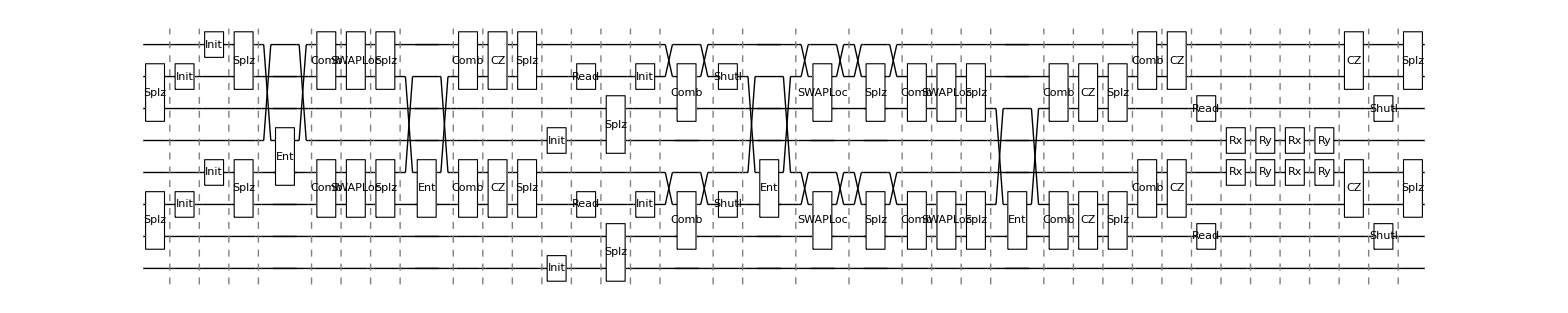

```mathematica
DrawCircuit@CircTrappedIons[circ,dev]
```

InsertCircuitNoise will update the device state. So, do it once. This will show the total scheduling, noise operation, and the final form in the simulation.
Set the MapQubits->False and ReplaceAliases->True if you intended to do the simulation

```mathematica
circ2=CircTrappedIons[circ,dev,MapQubits->False];
noisycirc=InsertCircuitNoise[circ2, dev, ReplaceAliases->True];
```

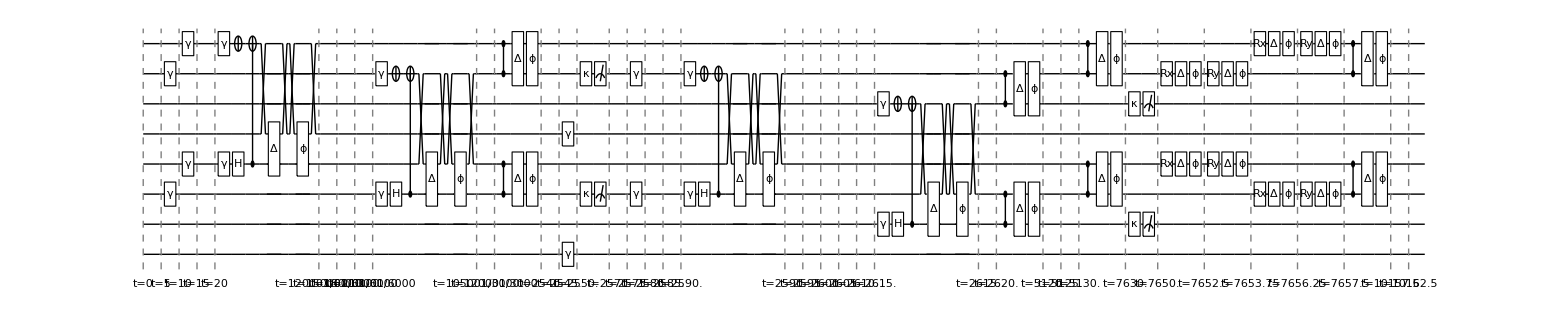

```mathematica
DrawCircuit[noisycirc]
```

The final arrangement after applying the circ

```mathematica
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
dev//Keys
```

{DeviceType,DeviceDescription,NumAccessibleQubits,NumTotalQubits,Nodes,QMap,ShowNodes,Aliases,Gates,DurationSymbol,Qubits}

```mathematica
dev[NumTotalQubits]
```

8

```mathematica
ρ=CreateDensityQureg[8];
```

```mathematica
(* initialise the qubit with random mixed state*)
SetQuregMatrix[ρ,RandomMixState[8]];
```

```mathematica
ApplyCircuit[ρ,ExtractCircuit@noisycirc];
```

```mathematica
PlotDensityMatrix@ρ
```

-Graphics3D-

```mathematica
dev@QMap
```

<|Alice→<|1→0,2→1,3→2,4→3|>,Bob→<|1→4,2→5,3→6,4→7|>|>

```mathematica
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
-1+Delete[Range[8],{{3},{7}}]
```

{0,1,3,4,5,7}

```mathematica
PlotDensityMatrix[PartialTrace[ρ,0,1,3,4,5,7],BarSpacing->0.1,ChartElementFunction->"Cube",ChartStyle->EdgeForm[Thick],PlotTheme->"Business"]
```

-Graphics3D-

[TODO:FUTURE FEATURES]

T1, and T2 for individual qubits
T1-><|”Alice”-><|1->100,2->101|>, “Bob”->110 |>,
modifyDev[dev,Opts->xxx]. One can modify T1, T2 in between.

Questlink takes initial indices; thus, passive noise is incorrect. Thus, passive noise is manually added for every gate.
Passive noise different on each zone.

Spatial move operations (SplitZ, CombS, PSwap) and quantum operations (the rest) must be done separately to follow the correct zone rules.
CombS, combine string within the zone not yet applied completely? (do one needs to combine string before applying 2-qubit gates?). Can one accidentally perform combine multiple times?  The noise on the move operations? (passive noise)

Correlated noise happens only to qubits with the same zone.

The role of measurement/outcome in the sequence?
Measurement involves scattering that can affect neighborhood atoms within raidus.

Exact operations on entangling (forget everything before, then assign it to 01+10

Parrallel -> None, Default (no operations in the same zone, always parallel Alice and Bob, Ent is always serial) , Full (Default+ parallel when in different zone)